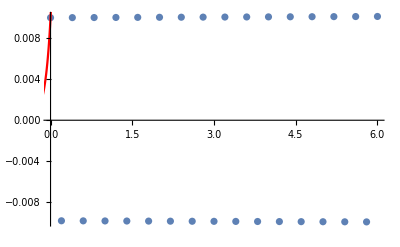

```mathematica
f[y_]:=10*y*(1-y);

logisticIC = 0.01;
logisticExact[t_] := 0.01/(0.01+0.99E^(-10t));

implicitEuiler[ic_,h_,T_] := (
Block[{n,y,x,i,explicitStep},
n = T/h;
y=Table[0,{i,0,n}];
x = Table[i*h,{i,0,n}];
y[[1]]= ic;
For[i=1,i<=n,++i,
explicitStep=y[[i]]+10*h*y[[i]](1-y[[i]]);
y[[i+1]]= yNext /. FindRoot[y[[i]]+10*h*yNext(1-yNext)==yNext,{yNext,explicitStep}];
];
Return[{y,
Table[{x[[i]],y[[i]]},{i,1,Length[x]}]}];
]
);

{y1,pt1}=implicitEuiler[logisticIC,0.2,6];

(*Plot[logisticExact[t,{t,0.1,6},PlotRange->{{0.6},{0,2}},PlotStyle->Red],ListPlot[pt1]];*)
plot = ListPlot[pt1];
(*Show[plot,Plot[u[t],{t,-1,1},PlotStyle->Red,PlotRange->{{-1,1},{-1,1}}]]*)
Show[plot, Plot[logisticExact[t],{t,-1,1},PlotRange->{{-1,1},{-1,1}},PlotStyle->Red]]
```

```mathematica
x /.FindRoot[x^2- 1== 0,{x,-1}]
```

-1.